```mathematica
bifurcation[dmin_,dmax_,nd_,gamma_,omega_,ndrop_,nplot_,psize_]:=(T=2*Pi/omega;
g[{xold_,vold_}]:={x[T],v[T]}/.NDSolve[{v'[t]==x[t]-x[t]^3-gamma*v[t]+A*Cos[omega*t],x'[t]==v[t],x[0]==xold,v[0]==vold},{x,v},{t,0,T}][[1]];
f[{x_,y_}]:={A,x};
ListPlot[Flatten[Table[f/@Drop[NestList[g,{1,0},nplot+ndrop],ndrop],{A,dmin,dmax,(dmax-dmin)/nd}],1],PlotStyle->{PointSize[psize],Hue[0],white},PlotRange->{{dmin,dmax},{-1.6,1.6}},AxesLabel->{"A","x"},AxesOrigin->{dmin,-1.6}])
bifurcation[0.30,0.35,200,0.1,1.4,1000,500,0.006]
```

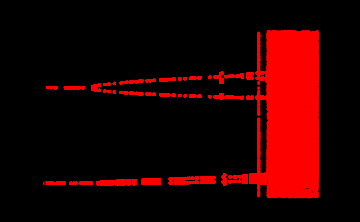

```mathematica
Show[%9,Background->Black]
```

```mathematica
Show[%9,Background->LightGray]
```

```mathematica
Rasterize[%7,"Image"]
```

-Graphics-